# Octagon

### Author

Eric W. Weisstein
July 3, 2018

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Octagon.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Octagon.html.

©2018 Wolfram Research, Inc. except for portions noted otherwise

## Examples

```mathematica
laminae=Select[EntityList[EntityClass["Lamina","Polygon"]],#["VertexCount"]==8&]
```

{regular octagon,inverted T-beam,square channel,square T-beam}

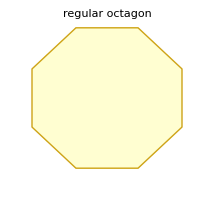
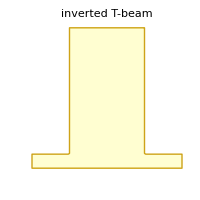
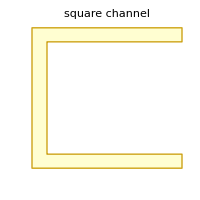
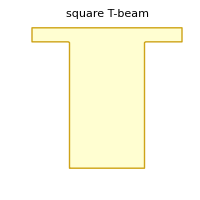

```mathematica
Show[#,PlotLabel->#2]&@@@EntityValue[laminae,{"Graphics","Name"}]
```

## Figure

```mathematica
polys={
Polygon[Entity["Lamina","FilledRegularOctagon"]["Vertices"][1]]->"regular octagon",
Polygon[Entity["Lamina","SquareTBeam"]["Vertices"][1,1.2,1,.2]]->"T-beam",
Polygon[Entity["Lamina","SquareChannel"]["Vertices"][.2,1,.8,1.2]]->"square channel",
Polygon[{{0,-1},{1,1},{2,-1},{3,1},{3,-1},{2,1},{1,-1},{0,1}}]->"butterfly octagon",
{Polygon[CirclePoints[.5,4]],Polygon[CirclePoints[4]]}->"square annulus"
};
```

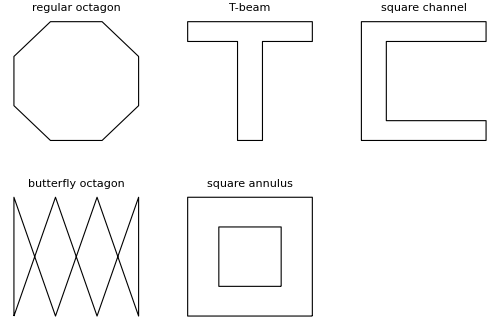

```mathematica
GraphicsGrid[Partition[
Graphics[{EdgeForm[Black],FaceForm[None],#},PlotLabel->Style[TextCell[#2,PageWidth->100,PageWidth->100],Directive[Italic,FontFamily->"Times"]]]&@@@polys,UpTo[3]],Spacings->50,ImageSize->500]
```